### Claim 1: Biological mechanisms are full of irreducibility

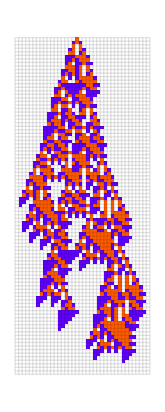

```mathematica
With[{ru={6006804516645,3,1}},GraphicsRow[
{RulePlot[CellularAutomaton[ru],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
MeshStyle->Opacity[.2],ImageSize->280],ArrayPlot[ArrayPad[CellularAutomaton[ru,{{1},0},94],{{0,0},{1,1}}],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]},Spacings->40]]
```

#### Case studies:

1. The genetic expression pathways that govern cell behavior

Relevant people:
Anna Greka Brood Institute (mapping genetic perturbations to rare kidney disease) 
Mohammed N AlQuraishi
- Formation of protein structure (unpredictable like our automata)
Action Items:
Meeting with Dr. Greka next week
Find lab with good dataset of these pathways
Understand AlQ’s work better
Sergey Ovchinnikov

2. The rules of cell movement, division and communication in morphogenesis
Relevant people:
Michael Levin:
- Experiment with frog embryo rearrangement
- Experiment with Planeria intervention
- Minimal model for morphogenesis as sorting algo
Eric Siggia (was at SF Bio Conf)
- Has mathematical model for morphogenesis in a particular organism I forget which.
Kieth Cheng (Penn State) zebrafish anatomy dataset):

```mathematica
$account = "blogannouncements";
$accountUserId = $account <> "@wolfram.com";
CloudConnect[$accountUserId, "SWWritingsP@55word"]
```

(phillip keller (https://www.janelia.org/lab/keller-lab))
 https://www.youtube.com/watch?v=R2I4c6C9Ths&t=2232s)

Action Items:
Find good minimal case study for embryo / morphogenesis where qualitative and quantitative measurements are possible

### Claim 1a: Structure arises out of necessity in a noisy environment:

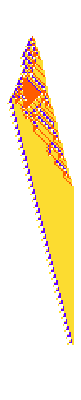

```mathematica
{{"[◼]", "PlotCA"}}[CellularAutomaton[{297413941736400589979939780692294751544,4,1}, {{1}, 0}, 200]]
```

#### Case studies:

1. Morphogenesis in non-embryotic developmental organisms like Planaria
Mike Levin again

2. Rules of adaptation in the human musculo-skeletal system
Andy Galpin
Marcus Elliiot Peak Performance Company
Nassim Taleb

3. Adaptation of sensory organs like the human eye
Andrew Huberman

4. Individual cell behavior

### Claim 2: Disease is what happens when the bounds on irreducibility fail:

```mathematica
GraphicsGrid[Partition[Table[{{"[◼]", "PlotCA"}}[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{150,{-8,36}},1]],"ArrowSize"->Small,"Trim"->{None,None},ImageSize->{Automatic,400}],{i,60}],15]]
```

-Graphics-

Action Items:
Find dataset of diseases, qualitative (images) and quantitative metrics

### Claim 2: Because of this irreducibility controlling these systems requires more detailed inputs and outputs

#### Case studies:

Immunotherapy